Part 4

```mathematica
ClearAll[k]
```

```mathematica
kb=1.38*10^-23
```

1.38×10^-23

```mathematica
(*exact function*)
```

```mathematica
exactF[J_,epsilon_,T_]:=(counter=0;
(*J=0.4;
epsilon=0.2;*)
Ns=ConstantArray[0,{32}];
energies=ConstantArray[0,{32}];
spins={0,0,0,0,0};
numerators={0,0,0,0,0,0};
PofN={{0,0},{1,0},{2,0},{3,0},{4,0},{5,0}};
FofN={{0,0},{1,0},{2,0},{3,0},{4,0},{5,0}};
Q=0;
For[i=-1,i≤1,i+=2,
	For[j=-1,j≤1,j+=2,
		For[k=-1,k≤1,k+=2,
			For[l=-1,l≤1,l+=2,
				For[m=-1,m≤1,m+=2,
				(*Print[i ,j, k, l, m];*)
					spins[[1]]=i;
					spins[[2]]=j; 
					spins[[3]]=k;
					spins[[4]]=l;
					spins[[5]]=m;
					ends = -J*spins[[1]]-J*spins[[5]];
					nnTerms=0;
					counter++;
					For[x=1,x≤4,x++,
						nnTerms += -J*spins[[x]]*spins[[x+1]];
					];
					tubeTerms=0;
					For[y=1,y≤5,y++,
						tubeTerms += (N[4*epsilon*spins[[y]]]-0);(*this was the problematic line*)
						Ns[[counter]]+=(spins[[y]]+1)/2;
	
					];
					(*Print[N[tubeTerms]];*)
					etot=nnTerms+ends+tubeTerms;
					energies[[counter]]=etot
					(*Print[nnTerms,"   ",  tubeTerms ,"   ",  ends];*)
				];
		];
	];
];
];
For[z=1,z≤32,z++,
(*Print[z,"      ",       energies[[z]],"    ",Exp[-1*energies[[z]]],"   ",Q];*)
Q+=Exp[-1*energies[[z]]];
numerators[[Ns[[z]]+1]]+=Exp[-1*energies[[z]]];
(*Print[energies[[z]]];*)
];
For[q=1,q≤6,q++,
PofN[[q]][[2]]=numerators[[q]]/Q;
(*FofN[[q]][[2]]=-kb*T*Log[PofN[[q]][[2]]];*)
FofN[[q]][[2]]=-Log[PofN[[q]][[2]]];
];
p=0;
Return[FofN];
)
```

```mathematica
(*estimated function*)
```

```mathematica
approxF[J_,epsilon_,T_]:=(counter=0;
(*J=0.4;
epsilon=0.2;*)
Ns=ConstantArray[0,{16}];
energies=ConstantArray[0,{16}];
spins={1,0,0,0,0,0,1};
numerators={0,0,0,0,0,0};
PofN={{0,0},{1,0},{2,0},{3,0},{4,0},{5,0}};
FofN={{0,0},{1,0},{2,0},{3,0},{4,0},{5,0}};
Q=0;
For[i=-1,i≤1,i+=2,
	For[j=-1,j≤1,j+=2,
		For[k=-1,k≤1,k+=2,
			For[l=-1,l≤1,l+=2,
				For[m=-1,m≤1,m+=2,
				(*Print[i ,j, k, l, m];*)
					spins[[2]]=i;
					spins[[3]]=j; 
					spins[[4]]=k;
					spins[[5]]=l;
					spins[[6]]=m;
					intCount = 0;
					For[y=1,y≤6,y++,
						If[spins[[y]]≠spins[[y+1]],intCount++]
					]
				If[intCount >2,Continue[]];
					counter++;
					(*Print[counter," ",i," ",j," ",k," ",l," ",m];*)
					ends = -J*spins[[2]]-J*spins[[6]];
					nnTerms=0;
					
					For[x=2,x≤5,x++,
						nnTerms += -J*spins[[x]]*spins[[x+1]];
					];
					tubeTerms=0;
					For[y=2,y≤6,y++,
						tubeTerms += (N[4*epsilon*spins[[y]]]-0);
						Ns[[counter]]+=(spins[[y]]+1)/2;
	
					];
					(*Print[N[tubeTerms]];*)
					etot=nnTerms+ends+tubeTerms;
					energies[[counter]]=etot
					(*Print[i," ",j," ",k," ",l," ",m,"         ",Ns[[counter]],"        ",nnTerms,"       ",tubeTerms,"       ",ends];*)
					(*Print[nnTerms,"   ",  tubeTerms ,"   ",  ends];*)
				];
		];
	];
];
];
For[z=1,z≤16,z++,
(*Print[Ns[[z]],"  ",energies[[z]]];*)
Q+=Exp[-1*energies[[z]]];
numerators[[Ns[[z]]+1]]+=Exp[-1*energies[[z]]];
(*Print[energies[[z]]];*)
];
For[q=1,q≤6,q++,
PofN[[q]][[2]]=numerators[[q]]/Q;
(*FofN[[q]][[2]]=-kb*T*Log[PofN[[q]][[2]]];*)
FofN[[q]][[2]]=-Log[PofN[[q]][[2]]];
];
Return[FofN];
)

test=approxF[0.4,0.04,200]
```

{{0,2.07392},{1,1.70077},{2,1.61531},{3,1.64762},{4,1.74448},{5,2.07392}}

```mathematica
test2=exactF[0.4,0.04,200]
```

{{0,6.21932×10^-21},{1,4.45928×10^-21},{2,3.99083×10^-21},{3,4.31259×10^-21},{4,5.31007×10^-21},{5,6.21932×10^-21}}

```mathematica
ClearAll[k]
```

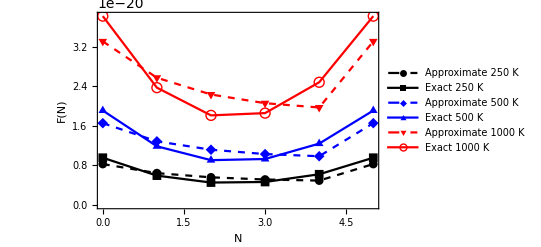

```mathematica
Compare2=ListLinePlot[{approxF[0.2,0.02,250],exactF[0.2,0.02,250],approxF[0.2,0.02,500],exactF[0.2,0.02,500],approxF[0.2,0.02,1000],exactF[0.2,0.02,1000]},PlotMarkers->Automatic,Frame->True,FrameLabel->{"N","F(N)"},PlotLegends->{"Approximate 250 K","Exact 250 K","Approximate 500 K","Exact 500 K","Approximate 1000 K","Exact 1000 K"},PlotStyle->{{Black,Dashed},Black,{Blue,Dashed},{Blue},{Red,Dashed},{Red}}]
```

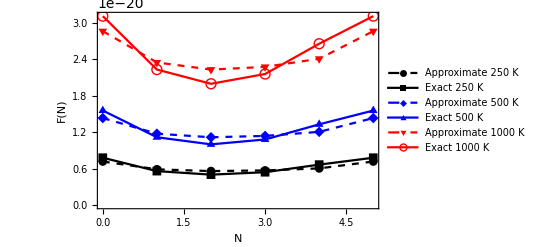

```mathematica
Compare4=ListLinePlot[{approxF[0.4,0.04,250],exactF[0.4,0.04,250],approxF[0.4,0.04,500],exactF[0.4,0.04,500],approxF[0.4,0.04,1000],exactF[0.4,0.04,1000]},PlotMarkers->Automatic,Frame->True,FrameLabel->{"N","F(N)"},PlotLegends->{"Approximate 250 K","Exact 250 K","Approximate 500 K","Exact 500 K","Approximate 1000 K","Exact 1000 K"},PlotStyle->{{Black,Dashed},Black,{Blue,Dashed},{Blue},{Red,Dashed},{Red}}]
```

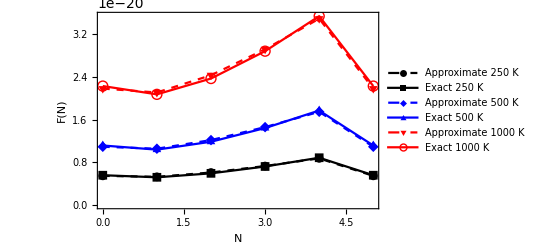

```mathematica
Compare8=ListLinePlot[{approxF[0.8,0.08,250],exactF[0.8,0.08,250],approxF[0.8,0.08,500],exactF[0.8,0.08,500],approxF[0.8,0.08,1000],exactF[0.8,0.08,1000]},PlotMarkers->Automatic,Frame->True,FrameLabel->{"N","F(N)"},PlotLegends->{"Approximate 250 K","Exact 250 K","Approximate 500 K","Exact 500 K","Approximate 1000 K","Exact 1000 K"},PlotStyle->{{Black,Dashed},Black,{Blue,Dashed},{Blue},{Red,Dashed},{Red}}]
```

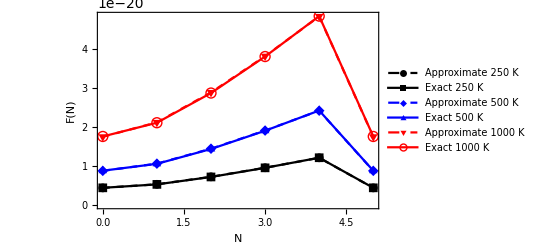

```mathematica
Compare12=ListLinePlot[{approxF[1.2,0.12,250],exactF[1.2,0.12,250],approxF[1.2,0.12,500],exactF[1.2,0.12,500],approxF[1.2,0.12,1000],exactF[1.2,0.12,1000]},PlotMarkers->Automatic,Frame->True,FrameLabel->{"N","F(N)"},PlotLegends->{"Approximate 250 K","Exact 250 K","Approximate 500 K","Exact 500 K","Approximate 1000 K","Exact 1000 K"},PlotStyle->{{Black,Dashed},Black,{Blue,Dashed},{Blue},{Red,Dashed},{Red}}]
```

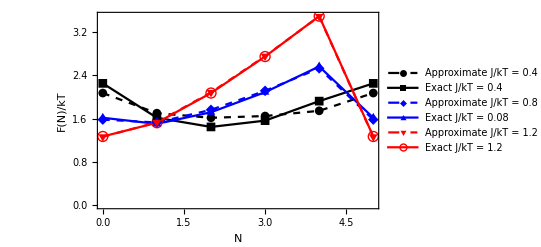

```mathematica
CompareNew = ListLinePlot[{approxF[0.4,0.04,250],exactF[0.4,0.04,250],approxF[0.8,0.08,500],exactF[0.8,0.08,500],approxF[1.2,0.12,1000],exactF[1.2,0.12,1000]},PlotMarkers->Automatic,Frame->True,FrameLabel->{"N","F(N)/kT"},PlotLegends->{"Approximate J/kT = 0.4", "Exact J/kT = 0.4", "Approximate J/kT = 0.8", "Exact J/kT = 0.08","Approximate J/kT = 1.2", "Exact J/kT = 1.2"},BaseStyle->{FontSize->14},PlotStyle->{{Black,Dashed},Black,{Blue,Dashed},{Blue},{Red,Dashed},{Red}}]
```

```mathematica
Export["/Users/rachelkrueger/Documents/StatMech/fig5.eps",CompareNew]
```

/Users/rachelkrueger/Documents/StatMech/fig5.eps